## 3. leaky accumulators

### (a)

```mathematica
f[x_,b_]:=1/(1+Exp[-4(x-b)])
term1=-x;
term2=a f[x,b];
xdot=term1+term2;
```

Fixed points are intersections of - term1 and term2.

```mathematica
bspesh=0.7;
```

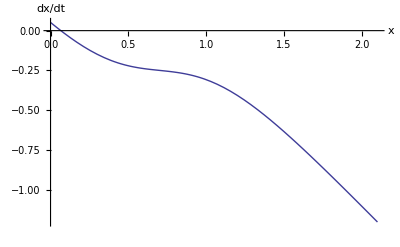

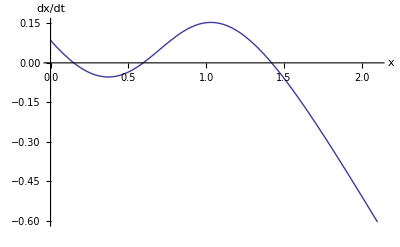

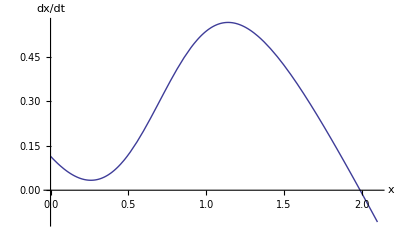

```mathematica
For[i=1,i<=3,i++,
aval = {.9, 1.5,2.0}[[i]];
Print[Plot[( xdot/.{a->aval,b->bspesh}),{x,0,2.1},
AxesLabel->{"x", "dx/dt"}]];
]
```

The first steady state is stable in the low-α case. Two new fixed points appear above a threshold value of  α. The left (central) one is unstable, and the right one stable. Eventually, the central fixed point collides with the left one, and only the right point remains. That is, a couple of 1D fold bifurcations.

Since this looks a lot like a cubic centered at b, let’s do a O(3) Taylor expansion there.

```mathematica
p=Normal[Series[xdot,{x,b,3}]]
```

a/2-b+(-1+a) (-b+x)-4/3 a (-b+x)^3

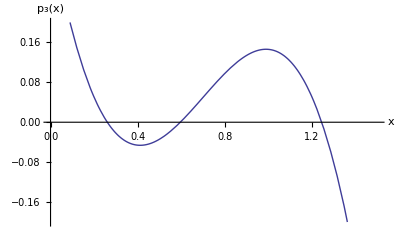

```mathematica
Plot[p/.{a->1.5,b->bspesh},{x,0,1.5},
PlotRange->{{0,1.5},{-.2,.2}},
AxesLabel->{"x","p_3(x)"}]
```

As a O(3) polynomial, this will always have 1 real root. The existince of other real roots can be found by the discriminant, Δ. If Δ>0, there are three distinct real roots. If Δ=0, there is one repeated real root and one distinct real root. If Δ<0, there is one real root and a complex conjugate pair.

-4/3 (4 a-12 a^2+12 a^3+5 a^4-36 a^3 b+36 a^2 b^2)

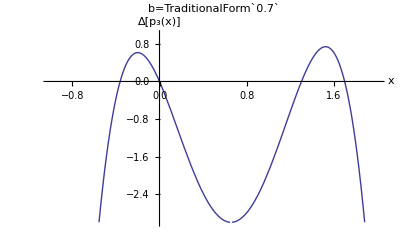

```mathematica
Δ=Discriminant[p,x]
Plot[((Δ)/.{b->bspesh}),{a,-1,2},
PlotRange->{{-1,2},{-3,1}},
AxesLabel->{"x","Δ[p_3(x)]"},
PlotLabel->StringForm["b=``",bspesh]]
```

This is an O(4) polynomial in α. However, we can factor out the α=0 root. Then, it just so happens that b=1/2 gives us a tangency (repeated real root for α). This gives both the “suitable range” (>1/2) for b and an explanation for why α>1 is a necessary but notsufficient condition for triple roots.

```mathematica
D2=Simplify[Δ/a,a≠0]
Solve[(D2/.{b->1/2})==0,a]
```

-4/3 (4+5 a^3+a^2 (12-36 b)+12 a (-1+3 b^2))

{{a→-4/5},{a→1},{a→1}}

```mathematica
linearMesh[a_,b_,n_Integer]:=Array[#&,n,{a,b}]
```

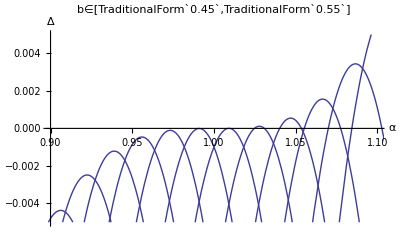

```mathematica
npts=12;
l=.5-.05;
r=.5+.05;
bvals=linearMesh[l,r,npts];
Plot[
Table[
Δ/.{b->bvals[[i]]},
{i,npts}
],
{a,-1,2},
AxesLabel->{"α","Δ"},
PlotRange->{{.9,1.1},{-.005,.005}},
(*PlotRange->{{.9,1.1},{-.1,.1}},*)
PlotLabel->StringForm["b∈[``,``]",l,r] 
]
aval=1.05;
```

For an α value just above 1, varying b around 1/2 gives a bifurcation diagram flipped from that in terms of α-- first there is a single, stable high - x root, then a pair of lower ones (stable, unstable) appear, then the central and upper fixed points disapppear. All (dis)apppearances occur locally-quadratically.

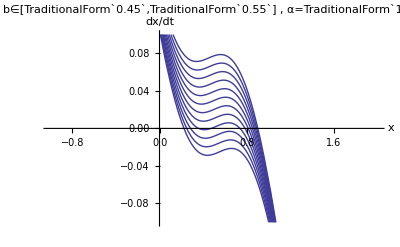

```mathematica
Plot[
Table[
xdot/.{a->aval}/.{b->bvals[[i]]},
{i,npts}
],
{x,-1,2},
AxesLabel->{"x","dx/dt"},
PlotRange->{Automatic,{-.1,.1}},
PlotLabel->StringForm["b∈[``,``]  ,  α=``",l,r,aval] 
]
```

```mathematica
Solve[Δ==0,a]
```

{{a→0},{a→4/5 (-1+3 b)-(-324+864 b-756 b^2)/(45 6^(1/3) (-39+156 b-228 b^2+108 b^3+5 √3 √(3-24 b+72 b^2-88 b^3+96 b^5-64 b^6))^(1/3))+1/5 6^(1/3) (-39+156 b-228 b^2+108 b^3+5 √3 √(3-24 b+72 b^2-88 b^3+96 b^5-64 b^6))^(1/3)},{a→4/5 (-1+3 b)+((1+ⅈ √3) (-324+864 b-756 b^2))/(90 6^(1/3) (-39+156 b-228 b^2+108 b^3+5 √3 √(3-24 b+72 b^2-88 b^3+96 b^5-64 b^6))^(1/3))-1/(5 2^(2/3))3^(1/3) (1-ⅈ √3) (-39+156 b-228 b^2+108 b^3+5 √3 √(3-24 b+72 b^2-88 b^3+96 b^5-64 b^6))^(1/3)},{a→4/5 (-1+3 b)+((1-ⅈ √3) (-324+864 b-756 b^2))/(90 6^(1/3) (-39+156 b-228 b^2+108 b^3+5 √3 √(3-24 b+72 b^2-88 b^3+96 b^5-64 b^6))^(1/3))-1/(5 2^(2/3))3^(1/3) (1+ⅈ √3) (-39+156 b-228 b^2+108 b^3+5 √3 √(3-24 b+72 b^2-88 b^3+96 b^5-64 b^6))^(1/3)}}

### (b)

```mathematica
x1dot=-x1+a f[x1,b1]-b f[x2,b2]+s1;
x2dot=-x2+a f[x2,b2]-b f[x1,b1]+s2;
(*Solve[{x1dot==0,x2dot==0},{x1,x2}]*)
```

```mathematica
simpleParams={s1->1.1,s2->1,a->1.05,b->1.05,b1->.55,b2->.55};
```

```mathematica
x1dot/.simpleParams
```

1.1+1.05/(1+ⅇ^(-4 (-0.55+x1)))-1.05/(1+ⅇ^(-4 (-0.55+x2)))-x1

```mathematica
Print[Plot3D[
{
x1dot/.simpleParams,
x2dot/.simpleParams,
0
},
{x1,0,3},{x2,0,3},
Mesh->None,
PlotStyle->{
{Red,Opacity[.8],Specularity[White,100]},
{Green,Opacity[.8],Specularity[White,100]},
{Blue,Opacity[0.5]}
},
AxesLabel->{"x_1","x_2","dx_1/dt and dx_2/dt"},
ImageSize->Large
]];
```

-Graphics3D-

```mathematica
x1null=Flatten[Assuming[C[1]∈Integers,Simplify[Solve[x1dot==0,x2]]]/.{C[1]->0}/.simpleParams]
```

{x2→0.55-1/4 Log[(-1.05 ⅇ^(4 x1)+1.05 (9.02501+ⅇ^(4 x1))+(9.02501+ⅇ^(4 x1)) (-1.1+x1))/(1.05 ⅇ^(4 x1)+(9.02501+ⅇ^(4 x1)) (1.1-x1))]}

```mathematica
implot2[f_,domain_]:=(
p1=Plot[
Re[f],
domain,
PlotLegends->{"real"},
PlotStyle->{Red}
];
p2=Plot[
Im[f],
domain,
PlotLegends->{"imaginary"},
PlotStyle->{Blue}
];
Return[Show[p1,p2,AxesLabel->{domain[[1]]}]];
)
```

0.55-1/4 Log[(0.451251+ⅇ^(4 x1) (1.1-1. x1)-9.02501 x1)/(-9.92751+ⅇ^(4 x1) (-2.15+x1)+9.02501 x1)]

x1 nullcline: x2 vs x1

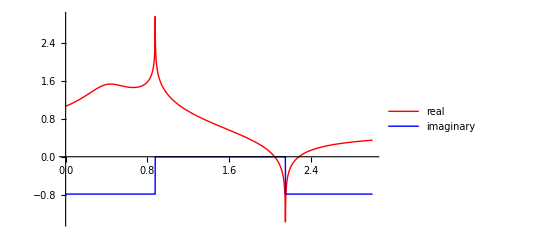

0.55-1/4 Log[(-0.451251+ⅇ^(4 x2) (1.-1. x2)-9.02501 x2)/(-9.02501+ⅇ^(4 x2) (-2.05+x2)+9.02501 x2)]

x2 nullcline: x1 vs x2

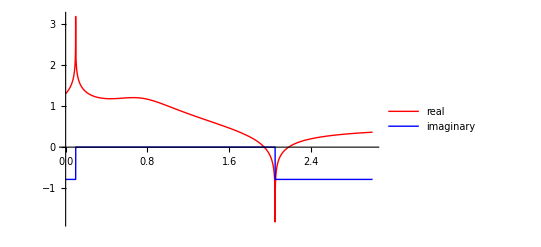

```mathematica
plots={};
nulls={};
For[i=1,i≤2,i++,
dot={x1dot,x2dot}[[i]];
thisvar={x1,x2}[[i]];
othervar={x2,x1}[[i]];
subs=(
Flatten[Assuming[C[1]∈Integers,Simplify[
Solve[dot==0,othervar
]]/.{C[1]->0}/.simpleParams]
]
);
null=Simplify[othervar/.subs];
Print[null];
Print[StringForm["`` nullcline: `` vs ``",thisvar,othervar,thisvar]];
plot=implot2[
null,
{thisvar,0,3}
];
Print[plot];
AppendTo[plots,plot];
AppendTo[nulls,null];
];
```

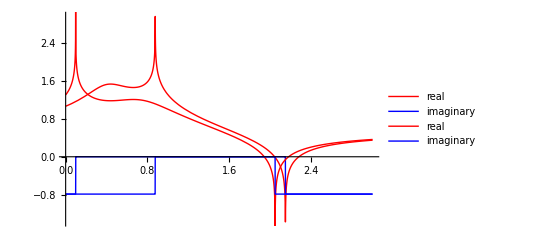

```mathematica
Show[plots]
```

```mathematica
Solve[nulls[[1]]==nulls[[2]],x1]
```

Solve::inex: Solve was unable to solve the system with inexact coefficients or the system obtained by direct rationalization of inexact numbers present in the system. Since many of the methods used by Solve require exact input, providing Solve with an exact version of the system may help.

Solve[0.55-1/4 Log[(0.451251+ⅇ^(4 x1) (1.1-1. x1)-9.02501 x1)/(-9.92751+ⅇ^(4 x1) (-2.15+x1)+9.02501 x1)]==0.55-1/4 Log[(-0.451251+ⅇ^(4 x2) (1.-1. x2)-9.02501 x2)/(-9.02501+ⅇ^(4 x2) (-2.05+x2)+9.02501 x2)],x1]